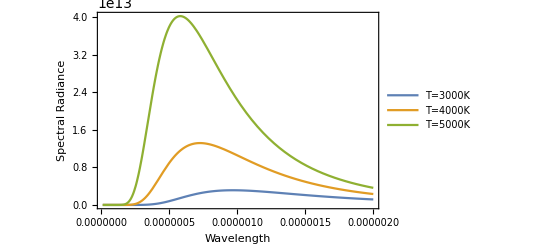

```mathematica
(* Blackbody Radiation Spectrum *)
h=6.626*10^-34;
c=3*10^8;
kB=1.381*10^-23;
PlanckRadiation[λ_,T_]:=(2 Pi h c^2)/λ^5*1/(Exp[(h c)/(λ kB T)]-1);

Plot[Evaluate@Table[PlanckRadiation[λ,T],{T,{3000,4000,5000}}],{λ,10^-8,2*10^-6},Frame->True,PlotLegends->{"T=3000K","T=4000K","T=5000K"},AxesLabel->{"Wavelength","Spectral Radiance"},PlotRange->All]
```

```mathematica
(* Dispersion in Quantum Mechanics *)
eqn=I D[ψ[x,t],t]==-1/2D[ψ[x,t],{x,2}];
sol[x_,t_]=DSolveValue[{eqn,ψ[x,0]==Exp[-x^2]},ψ[x,t],{x,t}]//FullSimplify
Manipulate[Plot[Abs[sol[x,t]],{x,-10,10},PlotRange->{0,1},PlotTheme->"Scientific",ImageSize->Medium],{t,0,5,Appearance->"Labeled"}]

movsol[x_,t_]=DSolveValue[{eqn,ψ[x,0]==Exp[-x^2+1I x]},ψ[x,t],{x,t}]//FullSimplify
Manipulate[Plot[Abs[movsol[x,t]],{x,-10,10},PlotRange->{0,1},PlotTheme->"Scientific",ImageSize->Medium],{t,0,5,Appearance->"Labeled"}]
```

ConditionalExpression[-(ⅇ^(x^2/(-1-2 ⅈ t)) (ⅈ √((-ⅈ+2 t)^2) Erf[x/(√(-1-2 ⅈ t))]+(-ⅈ+2 t) (-2 ⅈ+Erfi[x/(√(1+2 ⅈ t))])))/(2 (1+2 ⅈ t)^(3/2)), Im[t]<1/2]

ConditionalExpression[(ⅇ^((t-2 x-2 ⅈ x^2)/(2 ⅈ-4 t)) (2 √(-ⅈ+2 t)+√(-ⅈ+2 t) Erf[(1+2 ⅈ x)/(2 √(1+2 ⅈ t))]+(-1)^(3/4) √(1+2 ⅈ t) Erf[((-1)^(1/4) (-ⅈ+2 x))/(2 √(-ⅈ+2 t))]))/(2 √(1+2 ⅈ t) √(-ⅈ+2 t)), Im[t]<1/2]

NDSolveValue::dsvar: -9.99959 cannot be used as a variable.

NDSolveValue::dsvar: -9.59143 cannot be used as a variable.

General::stop: Further output of NDSolveValue::dsvar will be suppressed during this calculation.

1-r/(2 a)

(ⅇ^(-r/(2 a)) (2 a-r))/(2 √2 a^(5/2))

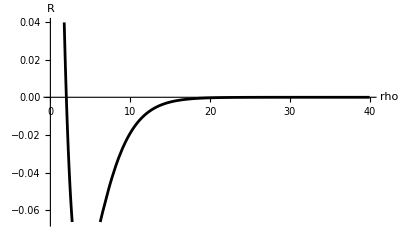

-1/32 ⅇ^(3 ⅈ phi) √(385/π) (-1+9 Cos[theta]^2) Sin[theta]^3

-Graphics3D-

```mathematica
(* Hydrogen Radial Function *)
ClearAll["Global`*"]
n=2;
l=0;
Hypergeometric1F1[(l-n+1),((2*l)+2),2*r/(n*a)]
R=Simplify[(1/a^(3/2))*(1/(((2*l)+1)!))*(2/n)^(3/2)*(((n+l)!)/(2*n*((n-l-1)!)))^(1/2)
*(2*r/(n*a))^l*E^(-r/(n*a))*Hypergeometric1F1[(l-n+1),((2*l)+2),2*r/(n*a)]]
a=1;
rho=r/a;
Plot[R,{r,0,40*a},Frame->False,AxesLabel->{"rho","R"},PlotStyle->{RGBColor[0,0,0],Thickness[.005]}]

(* Hydrogen Spherical Function *)
ClearAll["Global`*"]
l=5;
m=3;
p=SphericalHarmonicY[l,m,theta,phi]
a=Abs[p];
r=a^2;
x=r*Cos[phi]*Sin[theta];
y=r*Sin[phi]*Sin[theta];
z=r*Cos[theta];
ParametricPlot3D[{x,y,z},{theta, 0, Pi},{phi, 0, 2*Pi},PlotRange->All,Axes->False,Boxed->False,PlotPoints->100,Lighting->"Standard"]
```

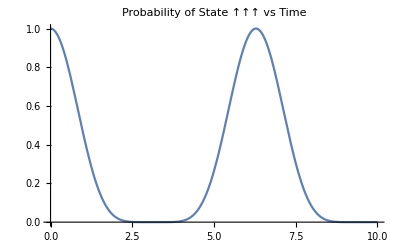

```mathematica
(* Time-dependent Solution of Heisenberg Hamiltonian (3 Spins) *)
σx={{0,1},{1,0}};
σy={{0,-I},{I,0}};
σz={{1,0},{0,-1}};
I2=IdentityMatrix[2];

J=1;h=.5;
H=-J (KroneckerProduct[σx,σx,I2]+KroneckerProduct[I2,σx,σx]+KroneckerProduct[σx,I2,σx]+KroneckerProduct[σy,σy,I2]+KroneckerProduct[I2,σy,σy]+KroneckerProduct[σy,I2,σy]+KroneckerProduct[σz,σz,I2]+KroneckerProduct[I2,σz,σz]+KroneckerProduct[σz,I2,σz])-h (KroneckerProduct[σx,I2,I2]+KroneckerProduct[I2,σx,I2]+KroneckerProduct[I2,I2,σx]);
ψ={1,0,0,0,0,0,0,0};
sol[t_]:=MatrixExp[-I H t].ψ;
prob[t_]:=Abs[sol[t]]^2;

Plot[prob[t][[1]],{t,0,10},PlotLabel->"Probability of State ↑↑↑ vs Time"]
```

```mathematica
(* 2D Particle in a box *)
Manipulate[Plot3D[(2/L) Sin[n π x/L] Sin[m π y/L],{x,0,L},{y,0,L},AxesLabel->{"x","y","ψ"},Mesh->None,ColorFunction->"DeepSeaColors",PlotPoints->100],{{n,2},1,5,1},{{m,3},1,5,1},{{L,1},0.5,2}]
```

```mathematica
(* Quantum Harmonic Oscillator *)
Manipulate[Module[{ξ=Sqrt[m ω/ħ] x},ψn[x_]:=HermiteH[n,ξ] Exp[-ξ^2/2];
Plot[ψn[x],{x,-5,5}]],{{n,6},0,6,1},{{m,1},0.5,5},{{ω,1},0.5,5},{{ħ,1},0.1,2}]
```